## This Mathematica notebook processes data from computer simulations and generates Figures 4ABF

### Run all cells sequentially unless only a specific figure is required but in such a case please note that some previous cells must also be executed.

```mathematica
SetDirectory[NotebookDirectory[]];
Needs["ErrorBarPlots`"]
Needs["ErrorBarLogPlots`"] (* this has to be installed separately*)
Clear[SE]
SE[x_]:=If[Length[x]>1,Sqrt[Variance[x]/Length[x]],0]
```

General::obspkg: ErrorBarPlots` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

```mathematica
Clear[FrontExample];
FrontExample[name_]:=Module[{str,nn,what,data,ymin,ymax,bn,tmp,ww,color},
If[FileExistsQ[name]==False,Print["file not found"];Interrupt[]];
str=OpenRead[name];
tmp=Read[str,{Number,Number,Number,Number,Number}];
nn=tmp[[1]];
ww=tmp[[4]];
what=Table[Number,{i,13}];
data=Table[Read[str,what],{i,nn}];
Close[str];
(*Do[data[[i,1]]=i,{i,Length[data]}];*)
ymin=Min[-data[[All,5]]]-3;ymax=Max[-data[[All,5]]]+3;
SeedRandom[1234];
If[Max[data[[All,1]]]<=1,color={Green,RGBColor[0.8,0,0.8]},color=Table[Hue[RandomReal[],0.25+0.75RandomReal[],1],{i,Max[data[[All,1]]]+1}]];
Graphics[Flatten[{Thickness->0.8/ww,CapForm->"Round",Table[{color[[1+data[[i,1]]]],Line[{{x+d Cos[ϕ],-y-d Sin[ϕ]},{x-d Cos[ϕ],-y+d Sin[ϕ]}}/.{x->data[[i,4]],y->data[[i,5]],ϕ->data[[i,10]],d->data[[i,12]]}]},{i,Length[data]}]}],ImageSize->600,PlotRange->{{-ww/2,ww/2},{ymin,ymax}},Background->Black]
]
```

## Fig. 4A

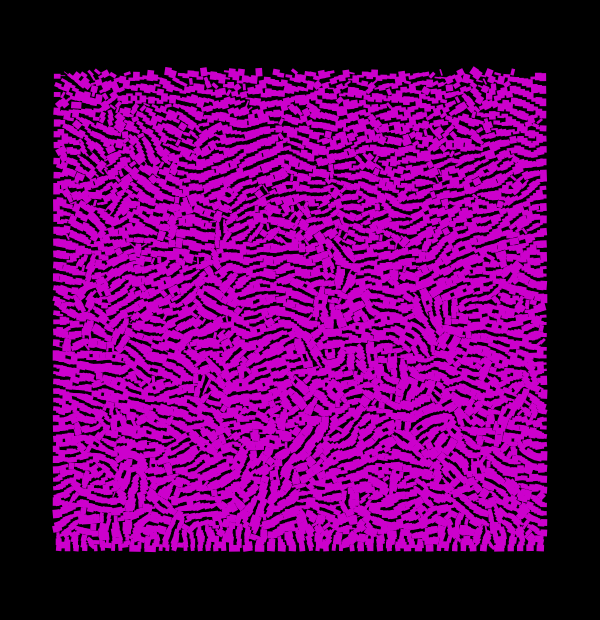

```mathematica
FrontExample[NotebookDirectory[]<>"\\data_Fig_4\\100x110_no_adh_shorter_10reps_s05_1in10_P10_A0\\data_1_0.dat"]
Export[NotebookDirectory[]<>"\\data_Fig_4\\4a1.png",%,"PNG"]
```

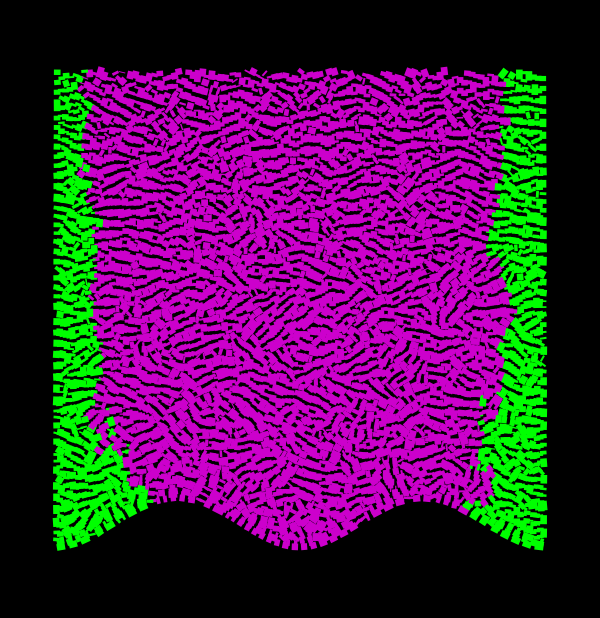

```mathematica
FrontExample[NotebookDirectory[]<>"\\data_Fig_4\\100x110_no_adh_shorter_10reps_s05_1in10_P50_A5\\data_1_4.dat"]
Export[NotebookDirectory[]<>"\\data_Fig_4\\4a2.png",%,"PNG"]
```

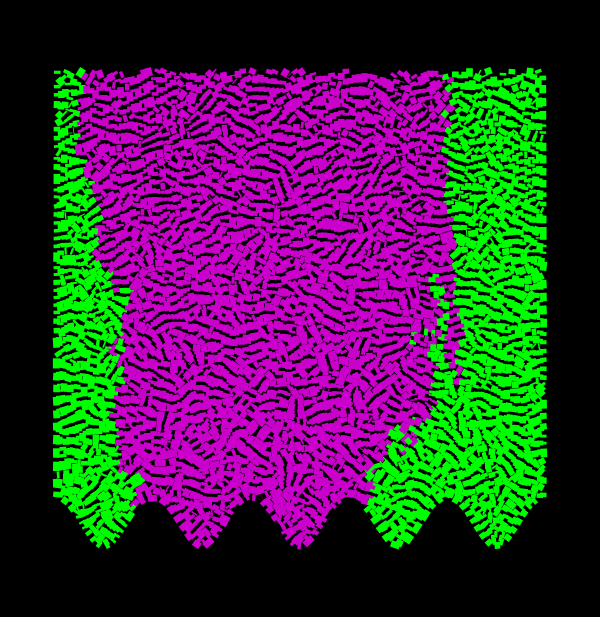

```mathematica
FrontExample[NotebookDirectory[]<>"\\data_Fig_4\\100x110_no_adh_shorter_10reps_s05_1in10_P20_A5\\data_1_2.dat"]
Export[NotebookDirectory[]<>"\\data_Fig_4\\4a3.png",%,"PNG"]
```

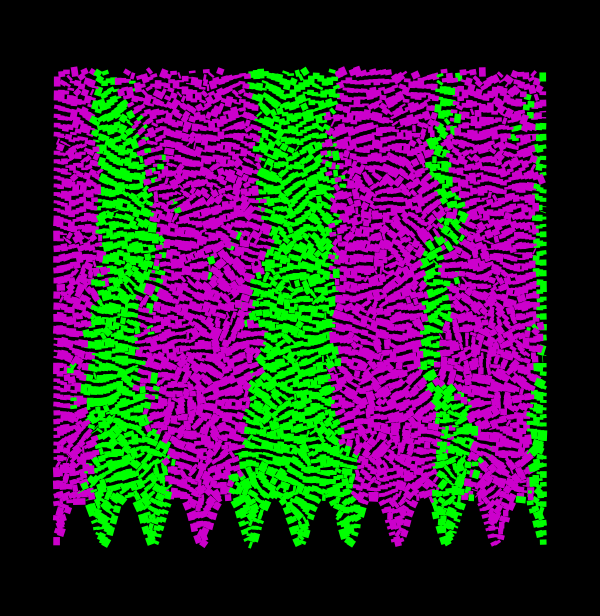

```mathematica
FrontExample[NotebookDirectory[]<>"\\data_Fig_4\\100x110_no_adh_shorter_10reps_s05_1in10_P10_A5\\data_1_0.dat"]
Export[NotebookDirectory[]<>"\\data_Fig_4\\4a4.png",%,"PNG"]
```

## Fig. 4 B

### simulations without adhesion

```mathematica
datasetnames=Reverse[{"100x110_no_adh_shorter_10reps_s05_1in10_P5_A5","100x110_no_adh_shorter_10reps_s05_1in10_P10_A5","100x110_no_adh_shorter_50reps_P20_A5","100x110_no_adh_shorter_50reps_P50_A5","100x110_no_adh_shorter_10reps_s05_1in10_P10_A0"}];
(* check if all data sets exist *)
lens=Length[FileNames[NotebookDirectory[]<>"\\data_Fig_4\\"<>#<>"\\types_*.dat"]]&/@datasetnames;
Do[If[lens[[i]]==0,Print["missing data set: ",datasetnames[[i]]];Interrupt[]],{i,Length[datasetnames]}]
```

```mathematica
Clear[AllelesEndPoint]
AllelesEndPoint[name_,type_]:=Module[{names,frames,secsizes,secfracs,sl},names=FileNames[NotebookDirectory[]<>"\\data_Fig_4\\"<>name<>"\\types_*.dat"];
frames=Table[Gather[ReadList[names[[i]],{Number,Number,Number,Number}],(#1[[1]]==#2[[1]])&],{i,Length[names]}];Print[Length[frames]," ",Length[#]&/@frames];
frames=Select[frames,(Length[#]>50)&];(* select only runs that have finished *)
secsizes=Table[frames[[i,-1,All,4]],{i,Length[frames]}];
secfracs=Table[sl=Select[frames[[i,-1]],(#[[2]]==type)&][[All,4]];If[Length[sl]==0,sl={0}];sl/Total[frames[[i,-1,All,4]]],{i,Length[frames]}];
{Mean[1.Length[#]&/@secsizes],SE[1.Length[#]&/@secsizes],Mean[Flatten[1.secsizes]],SE[Flatten[1.secsizes]],Mean[Flatten[1.secfracs]],SE[Flatten[1.secfracs]]}
]
alleles0=MapIndexed[Join[#2,AllelesEndPoint[#1,0]]&,datasetnames]
all0noadh=alleles0[[All,{6,7}]];
```

10 {73,73,73,73,73,73,73,73,73,73}

50 {73,73,72,73,73,72,72,73,73,73,73,72,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,72,73,73,73,73,73,73,73,73,73,72,73,73,73,73}

50 {73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73}

10 {73,73,73,73,73,73,73,73,73,73}

10 {73,73,73,73,73,73,73,73,73,73}

{{1,1.1,0.1,6620.36,637.907,0.00345545,0.00345545},{2,1.72,0.0641427,3592.58,231.77,0.442794,0.0540227},{3,1.96,0.0279942,3166.64,128.37,0.382872,0.0250564},{4,1.8,0.133333,3308.06,325.276,0.675839,0.0714442},{5,1.9,0.1,3038.53,358.173,0.75944,0.0388753}}

### simulations for adhesion to the substrate:

```mathematica
datasetnames={"100x110_adh_bs_1e6_02_s05_1in10_P10_A0","100x110_adh_bs_1e6_02_s05_1in10_P50_A5","100x110_adh_bs_1e6_02_s05_1in10_P20_A5","100x110_adh_bs_1e6_02_s05_1in10_P10_A5"};
(* check if all data sets exist *)
lens=Length[FileNames[NotebookDirectory[]<>"\\data_Fig_4\\"<>#<>"\\types_*.dat"]]&/@datasetnames;
Do[If[lens[[i]]==0,Print["missing data set: ",datasetnames[[i]]];Interrupt[]],{i,Length[datasetnames]}]
```

```mathematica
Clear[AllelesEndPoint]
AllelesEndPoint[name_,type_]:=Module[{names,frames,secsizes,secfracs,sl},names=FileNames[NotebookDirectory[]<>"\\data_Fig_4\\"<>name<>"\\types_*.dat"];
frames=Table[Gather[ReadList[names[[i]],{Number,Number,Number,Number}],(#1[[1]]==#2[[1]])&],{i,Length[names]}];Print[Length[frames]," ",Length[#]&/@frames];
frames=Select[frames,(Length[#]>50)&];(* select only runs that have finished *)
(*Print[Table[Select[frames[[i,-1]],(#[[2]]==type)&][[All,4]],{i,Length[frames]}]];*)
secsizes=Table[frames[[i,-1,All,4]],{i,Length[frames]}];
secfracs=Table[sl=Select[frames[[i,-1]],(#[[2]]==type)&][[All,4]];If[Length[sl]==0,sl={0}];sl/Total[frames[[i,-1,All,4]]],{i,Length[frames]}];
{Mean[1.Length[#]&/@secsizes],SE[1.Length[#]&/@secsizes],Mean[Flatten[1.secsizes]],SE[Flatten[1.secsizes]],Mean[Flatten[1.secfracs]],SE[Flatten[1.secfracs]]}
]
alleles0=MapIndexed[Join[#2,AllelesEndPoint[#1,0]]&,datasetnames]
alleles01=alleles0
```

10 {73,73,73,73,73,73,73,73,73,73}

10 {73,73,73,73,73,73,73,73,73,73}

10 {73,73,73,73,73,73,73,73,73,73}

«1 more identical outputs»

{{1,1.7,0.152753,4063.29,532.367,0.513187,0.120399},{2,1.8,0.133333,3418.72,417.846,0.66218,0.0925734},{3,2.,0.,3112.8,301.846,0.535664,0.0688825},{4,1.7,0.152753,3566.53,288.98,0.680582,0.0726769}}

{{1,1.7,0.152753,4063.29,532.367,0.513187,0.120399},{2,1.8,0.133333,3418.72,417.846,0.66218,0.0925734},{3,2.,0.,3112.8,301.846,0.535664,0.0688825},{4,1.7,0.152753,3566.53,288.98,0.680582,0.0726769}}

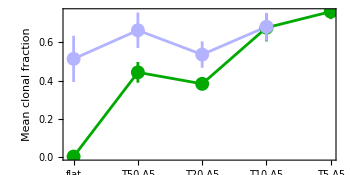

```mathematica
Show[ListPlot[{MapIndexed[{#2[[1]],#1}&,all0noadh[[All,1]]],MapIndexed[{#2[[1]],#1}&,alleles0[[All,6]]]},Joined->True,PlotStyle->{{Darker[Green],AbsolutePointSize[10],AbsoluteThickness[2]},{RGBColor[0.7,0.7,1],AbsolutePointSize[10],AbsoluteThickness[2]}}],ErrorListPlot[{all0noadh,alleles0[[All,{6,7}]]},PlotRange->All,PlotStyle->{{Darker[Green],AbsolutePointSize[10],AbsoluteThickness[2]},{RGBColor[0.7,0.7,1],AbsolutePointSize[10],AbsoluteThickness[2]}}],BaseStyle->{FontSize->18},Frame->True,FrameLabel->{None,"Mean clonal fraction"},FrameTicks->{{Automatic,None},{{{1,"flat"},{2,"T50 A5"},{3,"T20 A5"},{4,"T10 A5"},{5,"T5 A5"}},None}},ImageSize->350,AspectRatio->0.5,FrameStyle->{Black,AbsoluteThickness[2]}]
```

## Fig. 4 F

```mathematica
Clear[AllelesEndPoint]
ProcessDataVerbose=True;
AllelesEndPoint[name_,type_]:=Module[{names,frames,secsizes,secfracs,sl,ti,framelengths},names=FileNames[NotebookDirectory[]<>"\\data_Fig_4\\"<>name<>"\\types_*.dat"];
frames=Table[Gather[ReadList[names[[i]],{Number,Number,Number,Number}],(#1[[1]]==#2[[1]])&],{i,Length[names]}];
framelengths=Length[#]&/@frames;
If[ProcessDataVerbose,Print[Length[frames]," max_len=",Max[framelengths]," n=",Count[framelengths,Max[framelengths]]]];
frames=Select[frames,(Length[#]>90)&];(* select only runs that have finished *)
(*Print[Table[Select[frames[[i,-1]],(#[[2]]==type)&][[All,4]],{i,Length[frames]}]];*)
ti=-1;(* index of the frame for which the numbers will be calculated *)
secsizes=Table[frames[[i,ti,All,4]],{i,Length[frames]}];
secfracs=Table[sl=Select[frames[[i,ti]],(#[[2]]==type)&][[All,4]];If[Length[sl]==0,sl={0}];sl/Total[frames[[i,ti,All,4]]],{i,Length[frames]}];
{Mean[1.Length[#]&/@secsizes],SE[1.Length[#]&/@secsizes],Mean[Flatten[1.secsizes]],SE[Flatten[1.secsizes]],Mean[Flatten[1.secfracs]],SE[Flatten[1.secfracs]]}
]
ProcessData[name_]:=Module[{lens,datasetnames,alleles0},
datasetnames=(name<>#)&/@{"P10_A0","P100_A5.1","P100_A9.5","P50_A4.6","P50_A8.7","P20_A3.3","P20_A5.1","P10_A1.3","P10_A1.7"};
(* check if all data sets exist *)
lens=Length[FileNames[NotebookDirectory[]<>"\\data_Fig_4\\"<>#<>"\\types_*.dat"]]&/@datasetnames;
Do[If[lens[[i]]==0,Print["missing data set: ",datasetnames[[i]]];Interrupt[]],{i,Length[datasetnames]}];
alleles0=MapIndexed[Join[#2,AllelesEndPoint[#1,0]]&,datasetnames];
alleles0[[All,{6,7}]]
]
```

### no adhesion

```mathematica
ProcessDataVerbose=False;
thdata={
{{dt->3,fr->1/10,seladv->-0.6,maxstrain->0.0,onrif->50-4,offrif->98-50},ProcessData["100x110_RIF_DT_3h_ini19h_no_adh_s08_1in10att0_sin_"]},
{{dt->3,fr->1/5,seladv->-0.6,maxstrain->0.0,onrif->50-4,offrif->98-50},ProcessData["100x110_RIF_DT_3h_ini19h_no_adh_s08_1in5att0_sin_"]},
{{dt->3,fr->1/2.5,seladv->-0.6,maxstrain->0.0,onrif->50-4,offrif->98-50},ProcessData["100x110_RIF_DT_3h_ini19h_no_adh_s08_1in2.5att0_sin_"]}
}
```

{{{dt→3,fr→1/10,seladv→-0.6,maxstrain→0.,onrif→46,offrif→48},{{0.213557,0.0302106},{0.300399,0.0487631},{0.281231,0.0442956},{0.325238,0.0416302},{0.424433,0.0527792},{0.348217,0.0462862},{0.637899,0.0383005},{0.357136,0.0414053},{0.437885,0.0423361}}},{{dt→3,fr→1/5,seladv→-0.6,maxstrain→0.,onrif→46,offrif→48},{{0.161885,0.0260711},{0.222526,0.0417818},{0.176029,0.0321397},{0.162083,0.0316586},{0.219486,0.0375045},{0.195406,0.0328339},{0.486583,0.0302604},{0.205387,0.0291971},{0.232574,0.0290548}}},{{dt→3,fr→0.4,seladv→-0.6,maxstrain→0.,onrif→46,offrif→48},{{0.0374287,0.0112971},{0.158778,0.0366361},{0.103436,0.0229526},{0.0678049,0.0170026},{0.106796,0.024032},{0.0833399,0.0144975},{0.217484,0.0234922},{0.0464503,0.0115525},{0.0641214,0.0107987}}}}

{0.739854,0.68112,0.49021,0.758862,0.665751,0.778475,0.804531,0.873022,0.856595}

{{1,0.104835,0.0207944},{2,0.178017,0.0391151},{3,0.0828092,0.0144568},{4,0.128404,0.0294663},{5,0.131124,0.0288454},{6,0.16853,0.0324331},{7,0.443637,0.0324694},{8,0.281551,0.0377968},{9,0.296011,0.0366724}}

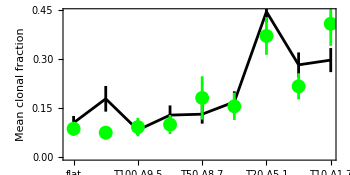

```mathematica
expdata={{1,0.08671934, 0.02098849},{2,0.07488334, 0.02011255},{3,0.091954, 0.02808793},{4,0.09958946, 0.0290632},{5,0.1806921, 0.06608351},{6,0.1550875 ,0.04161298},{7,0.36956947, 0.05742512},{8,0.21598324, 0.03986657},{9,0.40674572, 0.06739012}}; (* this is the clonal G fraction, not divided by initial fraction *)
iniGfrac={0.73985381, 0.68111988, 0.49020953, 0.75886208, 0.66575145, 0.77847535, 0.80453138, 0.87302154, 0.85659483} (* initial fractions of green cells at the end of 0.5ug/ml RIF *)
iniRfrac=1-iniGfrac;
mcnoadh08=Table[Module[{tmp,fitfrac,fiterr},tmp={fr/.#[[1]],#[[2,i,1]],#[[2,i,2]]}&/@thdata;
fitfrac=FindFit[tmp[[All,{1,2}]],a/(f+b),{{a,0.1},{b,0.1}},f];fiterr=FindFit[tmp[[All,{1,3}]],a+b f,{{a,0.1},{b,0.1}},f];{i,a/(f+b)/.fitfrac/.f->iniRfrac[[i]],a+b f/.fiterr/.f->iniRfrac[[i]]}],{i,Length[iniRfrac]}]
ErrorListPlot[{mcnoadh08,{{#[[1]],#[[2]]},ErrorBar[#[[3]]]}&/@expdata},PlotRange->All,BaseStyle->{FontSize->18},Joined->{True,False},PlotStyle->{{Black,AbsolutePointSize[10],AbsoluteThickness[2]},{Green,AbsolutePointSize[10],AbsoluteThickness[2]}},Frame->True,FrameLabel->{None,"Mean clonal fraction"},FrameTicks->{{Automatic,None},{{{1,"flat"},{2,"T100 A5.1"},{3,"T100 A9.5"},{4,"T50 A4.6"},{5,"T50 A8.7"},{6,"T20 A3.3"},{7,"T20 A5.1"},{8,"T10 A1.3"},{9,"T10 A1.7"}},None}},ImageSize->350,AspectRatio->0.5,FrameStyle->Black]
```

### with adhesion

```mathematica
ProcessDataVerbose=False;
thdata={
{{dt->3,fr->1/10,seladv->-0.6,maxstrain->0.0,onrif->50-4,offrif->98-50},ProcessData["100x110_RIF_DT_3h_ini19h_adh_1e6_005_s08_1in10att0_sin_"]},
{{dt->3,fr->1/5,seladv->-0.6,maxstrain->0.0,onrif->50-4,offrif->98-50},ProcessData["100x110_RIF_DT_3h_ini19h_adh_1e6_005_s08_1in5att0_sin_"]},
{{dt->3,fr->1/2.5,seladv->-0.6,maxstrain->0.0,onrif->50-4,offrif->98-50},ProcessData["100x110_RIF_DT_3h_ini19h_adh_1e6_005_s08_1in2.5att0_sin_"]}
}
```

{{{dt→3,fr→1/10,seladv→-0.6,maxstrain→0.,onrif→46,offrif→48},{{0.680901,0.0447277},{0.729048,0.0448721},{0.651487,0.0482595},{0.716887,0.039034},{0.767634,0.038616},{0.718003,0.0343064},{0.820941,0.0231387},{0.649632,0.0326933},{0.762886,0.029201}}},{{dt→3,fr→1/5,seladv→-0.6,maxstrain→0.,onrif→46,offrif→48},{{0.389447,0.0332573},{0.432524,0.044393},{0.447757,0.0519883},{0.577504,0.0384397},{0.560425,0.0367286},{0.539914,0.0352223},{0.673127,0.0279966},{0.416017,0.0323339},{0.576251,0.0324313}}},{{dt→3,fr→0.4,seladv→-0.6,maxstrain→0.,onrif→46,offrif→48},{{0.165757,0.0274745},{0.214369,0.0370427},{0.25907,0.0396151},{0.309626,0.0376761},{0.319236,0.0381236},{0.298383,0.0306672},{0.387222,0.0295266},{0.198168,0.0200739},{0.253631,0.0248845}}}}

```mathematica
expdata={{1,0.08671934, 0.02098849},{2,0.07488334, 0.02011255},{3,0.091954, 0.02808793},{4,0.09958946, 0.0290632},{5,0.1806921, 0.06608351},{6,0.1550875 ,0.04161298},{7,0.36956947, 0.05742512},{8,0.21598324, 0.03986657},{9,0.40674572, 0.06739012}}; (* this is the clonal G fraction, not divided by initial fraction *)
iniGfrac={0.73985381, 0.68111988, 0.49020953, 0.75886208, 0.66575145, 0.77847535, 0.80453138, 0.87302154, 0.85659483} (* initial fractions of green cells at the start of 1ug/ml RIF *)
iniRfrac=1-iniGfrac;
(*iniRfrac=Table[0.4,{9}];*)
mcadh=Table[Module[{tmp,fitfrac,fiterr},tmp={fr/.#[[1]],#[[2,i,1]],#[[2,i,2]]}&/@thdata;
fitfrac=FindFit[tmp[[All,{1,2}]],a/(f+b),{{a,0.1},{b,0.1}},f];fiterr=FindFit[tmp[[All,{1,3}]],a+b f,{{a,0.1},{b,0.1}},f];{i,a/(f+b)/.fitfrac/.f->iniRfrac[[i]],a+b f/.fiterr/.f->iniRfrac[[i]]}],{i,Length[iniRfrac]}]
```

{0.739854,0.68112,0.49021,0.758862,0.665751,0.778475,0.804531,0.873022,0.856595}

{{1,0.288404,0.0337207},{2,0.279706,0.0397398},{3,0.218634,0.0373496},{4,0.479295,0.0383487},{5,0.384225,0.0377813},{6,0.481503,0.0335598},{7,0.636311,0.0261549},{8,0.556172,0.033133},{9,0.639094,0.0304328}}

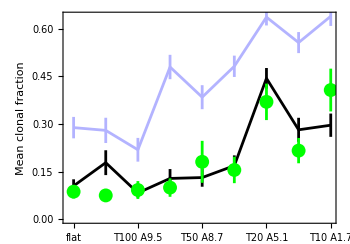

```mathematica
ErrorListPlot[{mcnoadh08,mcadh,{{#[[1]],#[[2]]},ErrorBar[#[[3]]]}&/@expdata},PlotRange->All,BaseStyle->{FontSize->18},Joined->{True,True,False},PlotStyle->{{Black,AbsolutePointSize[10],AbsoluteThickness[2]},{RGBColor[0.7,0.7,1],AbsolutePointSize[10],AbsoluteThickness[2]},{Green,AbsolutePointSize[10],AbsoluteThickness[2]}},Frame->True,FrameLabel->{None,"Mean clonal fraction"},FrameTicks->{{Automatic,None},{{{1,"flat"},{2,"T100 A5.1"},{3,"T100 A9.5"},{4,"T50 A4.6"},{5,"T50 A8.7"},{6,"T20 A3.3"},{7,"T20 A5.1"},{8,"T10 A1.3"},{9,"T10 A1.7"}},None}},ImageSize->350,AspectRatio->0.7,FrameStyle->Black]
```